```mathematica
Pattern[addition, {_,"+",_}]
```

addition:{_,+,_}

```mathematica
additionRules={__, "+",__}
```

{__,+,__}

```mathematica
MatchQ[{1, "+", 2}, additionRules]
```

True

```mathematica
commutativeGraph=[x, RelationGraph[commutativeAddition, {x,x}]][Range[100]](*Want to be able to define this functionally*)
```

```mathematica
commutativeGraph
```

commutativeGraph

```mathematica
MatchQ[1+2,2+1]
```

True

```mathematica
commutativeAddition[x_, y_]:=If[x+y==y+x, True, False]
```

```mathematica
algebra2PSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CK-12-Algebra-II-with-Trigonometry-Concepts_b_v78_eiy_s1.pdf", "Plaintext"]
```

1462420
 |  |  |  |

```mathematica
introAlgebraPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\scc_introductory_algebra_workbook_spring_2013.pdf", "Plaintext"];
```

```mathematica
calcPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CalcI_Complete_Problems.pdf", "Plaintext"]
```

Import::general: Expected cross reference table

Import::general: Could not find document trailer

General::stop: Further output of Import::general will be suppressed during this calculation.

```mathematica
a1QsPEMDAS={ "What is 2+2", "2+3","What is 2+3", "What is 1+1", "What is 20+22", "What is 1+15+21", "What is 33+5+8", "Simplify (2-5)^2", "Simplify 2-5^2", "Simplify 10-7+1", "Simplify 10-(7+1)", "Simplify 24/(4-2)^3", "Simplify 4+5(1+12/6)^2", "Simplify (15-3)/(1+5)", "1+12", "10% of 11", "30+40", "15+12", "20% of 33" , "11+12", "What is 5% of 100?"};
```

```mathematica
a1QsFractions={"express 3 2/7 as an improper fraction", "express 12 1/3 as an improper fraction", "Express 42/5 as a mixed number", "Express 53/9 as a mixed number", "write 3/18 in simplest form", "write 42/54 in simplest form" "What is 3 2/7 as an improper fraction","What is 12 1/3 as an improper fraction","What is 42/5 as a mixed number","What is 53/9 as a mixed number","What is 3/18 in simplest form","What is 42/54 in simplest form"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form"}
a1QsOppFrac={"Multiply 24/3 and 27/8", "Multiply 8 and 3/24", "Add 1/2 and 1/3", "What is  24/3 * 27/8", "What is  8 * 3/24", "What is  1/2 + 1/3"};
a1QsAbsoluteVal={"What is the absolute value of -1?", "What is |1|", "What is |-30|"};
a1QsNegatice={"What is 3-(-2)?", "What is -3+4"};
a1QsIntovars={"Evaluate a^2-b^2 when a=5 and b=3", "Evaluate a-b^2 when a=4 and b=2", "Evaluate a^2+b when a=7 and b=1"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form}

{Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form", }
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form,Null}

```mathematica
a1QsCombineLikeTerms={"Combine like terms of 3a-6a+10a-a", "Combine the like terms of 5x-10y+6z-3x", "Combine like terms of 3n-5n^2+6n-10+2n^2"};
```

```mathematica
a1QsDistrbutive={"5(2x+4)", "-3(x^2-2x+7)", "-(5x^4-8)"};
```

```mathematica
a1QsSolving={"8x-2=22", "-x-2=12", "2/3 x+3 =15"} ;
```

```mathematica
a1QsPolynomials={"Factor 3x^2+4x+1", "Factor n^2+5n+6", "Factor a^2+3a+2"};
```

```mathematica
a1QsPercent={"A $750 watch is on sale for 15% off. Find the sale price.", "A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?", "Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.", "A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.", 
"What is 10% of 100", "What is 4% of 16?", "200% of 3", "What is 45+300+4", "30+30", "90+200", "1+5", "34+1", "10% of 11", "5% of 112", "41+2" };
```

```mathematica
algebra1Questions=Flatten[{a1QsAbsoluteVal, a1QsCombineLikeTerms, a1QsDistrbutive, a1QsFractions, a1QsIntovars, a1QsPEMDAS, a1QsSolving, a1QsOppFrac, a1QsPercent, a1QsNegatice}];
```

```mathematica
algebra2PSetList[[8503;;8510]]
```

Part::take: Cannot take positions 8503 through 8510 in algebra2PSetList.

algebra2PSetList⟦8503;;8510⟧

```mathematica
algebra2Qs={"What is the most specific subset of the real numbers that -7 is a part of?", "Plot 1.25, 2/3 and 2 on a number line", "Identify the property used in the equations below as distributive, inverse or associative", "Evaluate 2x^2-9 for x=-3",  "Expand (a+b)^3", "What is (a+b)^n (Hint: What theorem is this?)", "Solve 4x-9=11", "Solve 3(x-5)+4=10", "Solve 3(x-5)+4=10", "Solve 9(x-3)+4=10", "Solve (x-1/2)=(2x+3)","Solve 3|x-5|=12","Solve 8(x-5)+4=10","Solve (x^2-5)=20",  "Use the law of sines to find the missing side of this triangle", "What is the largest value for the missing side of this triangle", "What is sin(60)", "What is tan(30)", "Write 30 degrees in radians", "Write π/4 in degrees", "Is x=-8 a solution to 1/2x+6>3?",  "Solve and graph the solution to 2x-3<7", "Solve and graph the solution to |3x-1|≥10",  "How many miutes are in a day?", "Wrie the standard form of y=3/2 x+2", "Write slope intercept form for a slope of 2 and y-intercept of 12", "Find a perpedicular line of y=3x+2 with y intercept of the origin","What are the domain and range of the trigonometric functions?" , "Graph the inequality y<3x+4", "Find the equation of best fit for the below listed data", "Graph the parabola give by x^2+3x+2. Find the zeros, vertex and intercept", "What is the sum from 1 to 5 of a=10n+3", "What is the next term in the series ", "what is the sum of the geometric series from 1 to infinity of 9(1/10)^n?", "What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?", "What is ln(1)?", "What are the domain and range of e^x and ln(x)", "sin(40)", "cos(45)", "tan(63)", "sin(121)", "sin(π/3)", "sin(π/5)", "cos(π/13)"};
```

```mathematica
calcQspcalc={"Evaluate f(x)=3-5x-2x^2 for the below values: f(0), f(x+h), f(6-t)", "Compute  the difrence quotient for the given function",  "Find the domain of (w^3-3w+1)/(12 w-7)","Find the inverse of f (x) = 6x +15", "Find inverse of W (x) =  (9 −11x)^(1/5)", "Find the exact value of cos(5 π/6) without using a calculator", "Find the exact value of sin(-4 π/3) without using a calculator", "Solve  4sin (3t ) = 2", "Solve 4sin (3t ) = 2 in [0, 4π/3], 2cos(x/3) +2^0.5 = 0 in [−7π ,7π }", "Solve 4y sec(7 y) = −21y", "Solve 3−14sin (12t + 7) =13", "Solve 3sec(4 − 9z) − 24 = 0", "Sketch the graph of f(x)=3^(1 + 2  x)", "Sketch the graph of h(x)=8+3e^(2  t - 4)",  "Determine ln(e^4)", "Combine 2 log_4x +5 log_4y - 1/2 log_4x" , "For the function W(x)=ln(1+x^4) and the point x=1, find the secants at point Q and the tangenet line", "For the function f(x)=(8-x^2)/(x^2-4), find the values at the below listed points and th limit as x aproaches 2",  , "For the function f(y)= sin(y)/y find the value at the below listed points and the limit as y approaches 0"};
```

```mathematica
calcQsderivs={"For the function f(x)=(8-x^2)/(x^2-4), use L'Hoptial's rule to find the limit as x aproaches 2",  "For the function (2-(t^2+3)^(1/2))/(t+1), L'Hoptial's rule to find the limit as x approaches -1", "Use the definition of the derivative to find the derivative of f(x)=6", "Use the definition of the derivative to find the derivative of V (t ) = 3−14t", 
 "Use the definition of the derivative to find the derivative of z(n)= (n+1)/(n+4)",
"Use the chain rule to find the derivative of Q(t)=(3t^3-4)^(1/2)", "Use the quotient rule to find the derivative of z(n)= (z+1)^(1/2)/(z+4)", 
"Find the deriviative of f (x) = 2cos(x) − 6sec(x) + 3", "Find the deriviative of g (z) =10 tan (z) − 2cot (z)", "Find the deriviative of  tan (w)sec(w)", "Find the deriviative of R(t)=(t+ tan(t))/(1+csc(t))", "Find the derivative of f(x)=2e^x-8^x", "Find the derivative of g(t)=4 log_3(t)-ln(t)", "Find the derivative of 2 cos(x)+arccos(x)" , "Find the derivative of x^2/y^3=1", "Find extrema of f(x)=12+6x^2-x^3", "Find extrema of g(w)=tan (w)sec(w)", "find the taylor expanision of g(w)=tan (w)sec(w) at w=π/4", "Find the MacLauren Expanision of z(n)= (z+1)^(1/2)/(z+4)", "Find the Derivative", "What is the Deriviative", "Evaluate the derivative", "Integral of ln(x) dx", "Integral of f(x)=x ln(x) from 0 to 10", "Integral of tan(x)", "Integral of (1+x)^(1/2)"};
```

```mathematica
calcQsIntegral={"Find ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7", "Evaluate ∫z^6 + 4z^4 − z^2 dz" ,"Determine f (x) given that f'(x) = 6x^8 − 20x^4 + x^2 + 9", "Find ∫ 2cos (w) − sec(w) tan (w)dw", "Find ∫12 + csc(θ ) [sin (θ ) + csc(θ )] dθ",
"What is ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7",
"What is the integral of sin(2x)?", "Find the area under the curve of |x| from -1 to 1", "What is the area under the curve sin^2x from 0 to π/2", "Find the integral", "What is the integral of x dx", "Derivative of f(x)=x^2", "Integral of x dx", "Integral of e^y dy", "Derivative of x^3", "Derivative of x", "Derivative of f(x)=20 ln(x)", "Derivative of x/(x+1)^2", "Derivative of x^n", "Derivative with respect to x", "Derivative of x^3"};
```

```mathematica
calcQs=Flatten[{calcQspcalc, calcQsIntegral, calcQsderivs}];
```

```mathematica
wpgRadicals=StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\WolframProblemGenerator-RadicalSummaryQuizKey.pdf", "Plaintext"]]
```

Import::general: Could not find the start of the cross reference table

Import::general: Expected cross reference table

Import::general: Could not find the start of the cross reference table

General::stop: Further output of Import::general will be suppressed during this calculation.

{}

```mathematica
wpgRadicals
```

{}

```mathematica
algebra2set=StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\algebra_2_set.pdf", "Plaintext"], {".)", "\n"}];
algebra2set[[2;;20;;7]]
```

{    9 + 3x + 7x = 39  \r,    - 6 + x + x = 14  \r,    - 5x + 7 + 6x = 18  \r}

```mathematica
AppendTo[algebra2Qs, algebra2set⟦2;;-1;;7⟧];
```

```mathematica
algebra2Qs=Flatten[algebra2Qs]; (*Algebra 2 eats eaverything now, but this is good, can do for the rest of the types*)
```

```mathematica
algebra1set:=StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\algebra_1_set.pdf", "Plaintext"], {".)",  "\n"}];
```

```mathematica
settoappend=algebra1set⟦2;;-1;;7⟧;
```

```mathematica
AppendTo[algebra1Questions, settoappend];
```

```mathematica
algebra1Questions=Flatten[algebra1Questions];
```

```mathematica
AppendTo[algebra1Questions, StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\Addition Question Generator.pdf", "Plaintext"], "\n"]];
```

```mathematica
algebra1Questions=Flatten[algebra1Questions];
```

```mathematica
algebra1Questions=Select[algebra1Questions, UnsameQ[#,{}]&]
```

{What is the absolute value of -1?,What is |1|,What is |-30|,Combine like terms of 3a-6a+10a-a,Combine the like terms of 5x-10y+6z-3x,Combine like terms of 3n-5n^2+6n-10+2n^2,5(2x+4),-3(x^2-2x+7),-(5x^4-8),express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form,Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1,What is 2+2,2+3,What is 2+3,What is 1+1,What is 20+22,What is 1+15+21,What is 33+5+8,Simplify (2-5)^2,Simplify 2-5^2,Simplify 10-7+1,Simplify 10-(7+1),Simplify 24/(4-2)^3,Simplify 4+5(1+12/6)^2,Simplify (15-3)/(1+5),1+12,10% of 11,30+40,15+12,20% of 33,11+12,What is 5% of 100?,8x-2=22,-x-2=12,2/3 x+3 =15,Multiply 24/3 and 27/8,Multiply 8 and 3/24,Add 1/2 and 1/3,What is  24/3 * 27/8,What is  8 * 3/24,What is  1/2 + 1/3,A $750 watch is on sale for 15% off. Find the sale price.,A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?,Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.,A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.,What is 10% of 100,What is 4% of 16?,200% of 3,What is 45+300+4,30+30,90+200,1+5,34+1,10% of 11,5% of 112,41+2,What is 3-(-2)?,What is -3+4,    x / - 5 = - 3  \r,    x / 6 = 5  \r,    x + 4 = 16  \r,    x + 6 = 8  \r,    x + 9 = 13  \r,    2 = x - 3  \r,    x - 1 = - 10  \r,    x + 4 = - 4  \r,9,10,11,12,13,14,15,16,\r,    - 7 + x = 2  \r,    x / 3 = 3  \r,    13 = x + 1  \r,    x + 8 = 12  \r,    x + 6 = 6  \r,    4x = - 44  \r,    x / 4 = 7  \r,    x + 8 = 3  \r,63,64,65,66,67,68,69,\r,    x + 4 = - 6  \r,    - 9 + x = - 5  \r,    6x = - 48  \r,    15 = x + 4  \r,    11 = x + 10  \r,    x - 2 = - 8  \r,    10 + x = 1  \r,116,117,118,119,120,121,122,123,\r,    7x = 0  \r,    7 + x = 13  \r,    - 3 = x + 2  \r,    x / 6 = 6  \r,    x / - 2 = 1  \r,    x + 2 = 3  \r,    x / 7 = 2  \r,    3 = x + 3  \r,    x + 2 = - 8  \r,    x + 5 = -1  \r,    x + 7 = 13  \r,    -1 + x = -1  \r,    12 = x + 7  \r,    x + 8 = 14  \r,186,187,188,189,190,191,192,\r,    x + 2 = 8  \r,    x + 7 = 18  \r,    x + 9 = 2  \r,    - 5x = - 10  \r,    x - 4 = 0  \r,    x - 2 = 3  \r,    - 9 + x = - 7  \r,239,240,241,242,243,244,245,246,\r,    x + 10 = 12  \r,    7 + x = 13  \r,    2x = 2  \r,    - 3 = x - 4  \r,    - 10 + x = 1  \r,    18 = x + 8  \r,    5 + x = 12  \r,    x - 5 = 7  \r,293,294,295,296,297,298,299,300,\r,    4x - 8 = 8  \r,    5x + 5 = 10  \r,    - 4x + 9 = - 27  \r,    10 + 5x = 10  \r,    6x - 3 = - 75  \r,    8 + 2x = 14  \r,    4x + 7 = 15  \r,362,363,364,365,366,367,368,369,\r,    10 + 5x = 60  \r,    - 5x - 2 = - 27  \r,    6x - 5 = 67  \r,    - 7x - 5 = - 26  \r,    7 - 7x = 63  \r,    7x + 6 = - 78  \r,    - 8 - 7x = 62  \r,    5x + 9 = -1  \r,416,417,418,419,420,421,422,423,\r,    5x - 9 = - 19  \r,    5x + 7 = - 33  \r,    6x + 7 = 25  \r,    3x - 6 = - 6  \r,    4 + 6x = 16  \r,    - 5 + 7x = 79  \r,    - 5x + 8 = 28  \r,    2x - 7 = 13  \r,470,471,472,473,474,475,476,\r,\r,\r,    2x + 8 = 10  \r,    3 - 3x = - 30  \r,    - 8 - 5x = 17  \r,    2x + 5 = - 7  \r,    3 + 4x = - 45  \r,    3x + 7 = 25  \r,    - 5x + 5 = 25  \r,537,538,539,540,541,542,543,    9 - 3x = - 21  \r,    4x - 9 = 19  \r,    6x + 1 = 61  \r,    - 2x + 8 = 32  \r,    10 + 3x = 10  \r,    2 - 2x = - 22  \r,    8 + 5x = 48  \r,587,588,589,590,591,592,593,4272 + 1001 \r,1570 + 5887 \r,8378 + 2232 \r,6719 + 9083 \r,7796 + 7881 \r,7333 + 2722 \r,6529 + 4391 \r,1521 + 2554 \r,8168 + 4402 \r,5750 + 9568 \r,9525 + 2244 \r,3160 + 1245 \r,\r,9577 + 7198 \r,9600 + 7472 \r,4781 + 7748 \r,2005 + 8361 \r,2143 + 8202 \r,1723 + 5702 \r,2729 + 6856 \r,8118 + 4430 \r,7438 + 3315 \r,1632 + 9300 \r,\r,5074 + 7065 \r,7949 + 9040 \r,\r,9361 + 9434 \r,2590 + 3048 \r,5035 + 9586 \r,2587 + 4970 \r,1726 + 9260 \r,9503 + 3152 \r,3434 + 9380 \r,9857 + 3068 \r,4027 + 2502 \r,1329 + 9063 \r,7272 + 6191 \r,8074 + 7521 \r,\r,1113 + 3615 \r,6987 + 5576 \r,5571 + 3857 \r,2940 + 6608 \r,2267 + 6108 \r,7900 + 6469 \r,2219 + 2574 \r,2433 + 5845 \r,\r,7946 + 9908 \r,8088 + 7921 \r,3661 + 5756 \r,6213 + 8955 \r,\r,5610 + 6137 \r,9618 + 8587 \r,3523 + 8800 \r,2420 + 4220 \r,8880 + 2001 \r,6379 + 2448 \r,1816 + 6956 \r,6178 + 2038 \r,2648 + 2854 \r,4832 + 1852 \r,7143 + 8177 \r,7524 + 7480 \r,\r,4662 + 2032 \r,9927 + 9121 \r,6639 + 6370 \r,8327 + 6129 \r,2757 + 2994 \r,3782 + 1330 \r,\r,6618 + 9094 \r,2259 + 6033 \r,3018 + 2248 \r,9532 + 5499 \r,9320 + 6116 \r,7748 + 4445 \r,\r,9422 + 5414 \r,9827 + 8472 \r,8158 + 7658 \r,1721 + 5812 \r,3850 + 4435 \r,7280 + 3811 \r,3109 + 7046 \r,7067 + 9862 \r,4116 + 6636 \r,7250 + 7530 \r,4154 + 9932 \r,\r,3928 + 9719 \r,7948 + 9978 \r,4741 + 6938 \r,4609 + 2756 \r,7498 + 1176 \r,\r,2968 + 7604 \r,3979 + 4765 \r,5465 + 9956 \r,2551 + 8585 \r,8088 + 3140 \r,5282 + 9116 \r,\r,8119 + 9714 \r,1664 + 8135 \r,2751 + 4607 \r,3880 + 6919 \r,2829 + 1933 \r,7988 + 5800 \r,9964 + 6451 \r,8932 + 7141 \r,8544 + 3707 \r,4910 + 8680 \r,4064 + 9078 \r,\r,3147 + 6538 \r,6703 + 2453 \r,1313 + 3009 \r,5840 + 1828 \r,8011 + 9651 \r,\r,5361 + 5519 \r,6669 + 6330 \r,4419 + 1814 \r,8784 + 3944 \r,4292 + 9179 \r,9474 + 9705 \r,6963 + 4488 \r,\r,6174 + 2651 \r,2390 + 5199 \r,5396 + 5061 \r,4261 + 8473 \r,9681 + 2776 \r,4880 + 1099 \r,9514 + 3323 \r,4447 + 4604 \r,8826 + 6933 \r,8059 + 1271 \r,7635 + 7934 \r,1692 + 5818 \r,\r,6842 + 8050 \r,6710 + 5531 \r,6682 + 8481 \r,\r,5893 + 2493 \r,7102 + 2281 \r,1383 + 3834 \r,7379 + 6677 \r,5626 + 9732 \r,5642 + 6535 \r,1985 + 4928 \r,1400 + 7429 \r,7665 + 3538 \r,\r,3021 + 8010 \r,6980 + 6177 \r,4918 + 3236 \r,5290 + 8994 \r,5980 + 1855 \r,8719 + 6369 \r,1750 + 5035 \r,7338 + 3228 \r,1570 + 8699 \r,7542 + 3349 \r,\r,6221 + 2277 \r,8325 + 1106 \r,9346 + 8468 \r,\r,3825 + 6015 \r,5219 + 1965 \r,4731 + 1603 \r,5571 + 5676 \r,6997 + 8056 \r,5465 + 8277 \r,4189 + 5839 \r,\r,5048 + 8140 \r,1531 + 4977 \r,1148 + 4232 \r,2087 + 5640 \r,5712 + 2107 \r,1967 + 3600 \r,6753 + 2906 \r,7131 + 1009 \r,6534 + 8733 \r,7614 + 5986 \r,\r,4270 + 9940 \r,4810 + 7408 \r,6775 + 7738 \r,5278 + 2794 \r,7136 + 8596 \r,\r,4420 + 6691 \r,5745 + 7730 \r,2943 + 8463 \r,2697 + 5880 \r,4764 + 7711 \r,4896 + 8505 \r,9300 + 2212 \r,\r,8759 + 8868 \r,5898 + 8735 \r,6671 + 7814 \r,8589 + 7764 \r,5930 + 4357 \r,2278 + 6186 \r,3096 + 2460 \r,9260 + 1150 \r,7982 + 5589 \r,3277 + 7411 \r,3740 + 4179 \r,2653 + 5175 \r,\r,1616 + 5751 \r,5519 + 6804 \r,1583 + 6324 \r,\r,8192 + 7500 \r,9043 + 3293 \r,7430 + 5558 \r,1630 + 8860 \r,7459 + 4738 \r,4096 + 5082 \r,1930 + 4841 \r,2815 + 5126 \r,4731 + 9595 \r,\r,0 + 2 \r,4 + 10 \r,6 + 2 \r,2 + 1 \r,9 + 0 \r,2 + 9 \r,9 + 7 \r,2 + 2 \r,8 + 10 \r,8 + 4 \r,9 + 6 \r,1 + 0 \r,\r,4 + 0 \r,\r,0 + 8 \r,4 + 0 \r,14 + 4 \r,10 + 33 \r,94 + 2 \r,39 + 10 \r,3 + 73 \r,45 + 0 \r,44 + 5 \r,4 + 55 \r,70 + 4 \r,\r,10 + 8 \r,4 + 0 \r,10 + 0 \r,5 + 4 \r,8 + 6 \r,90 + 8 \r,44 + 1 \r,66 + 2 \r,8 + 44 \r,68 + 4 \r,3 + 24 \r,\r,47 + 5 \r,\r,6 + 4 \r,3 + 4 \r,10 + 7 \r,9 + 10 \r,2 + 3 \r,6 + 7 \r,10 + 10 \r,5 + 1 \r,0 + 0 \r,20 + 3 \r,28 + 5 \r,48 + 2 \r,\r,10 + 29 \r,70 + 10 \r,63 + 0 \r,4 + 49 \r,78 + 10 \r,4 + 76 \r,50 + 5 \r,96 + 7 \r,3 + 90 \r,\r,5 + 88 \r,59 + 10 \r,41 + 2 \r,\r,16 + 6 \r,2 + 73 \r,6 + 13 \r,41 + 9 \r,2 + 14 \r,15 + 6 \r,35 + 7 \r,1 + 69 \r,4 + 83 \r,7 + 90 \r,4 + 74 \r,2 + 39 \r,\r,2 + 2 \r,9 + 7 \r,9 + 11 \r,3 + 11 \r,9 + 12 \r,0 + 86 \r,22 + 10 \r,\r,33 + 4 \r,9 + 39 \r,72 + 10 \r,0 + 95 \r,6 + 16 \r,\r,8 + 0 \r,4 + 9 \r,7 + 1 \r,3 + 10 \r,0 + 10 \r,10 + 29 \r,10 + 78 \r,3 + 13 \r,35 + 6 \r,10 + 1 \r,96 + 0 \r,3 + 38 \r,\r,1 + 1 \r,5 + 37 \r,10 + 69 \r,47 + 6 \r,94 + 5 \r,\r,10 + 83 \r,6 + 32 \r,30 + 1 \r,44 + 5 \r,7 + 15 \r,4 + 60 \r,1 + 14 \r,\r,5 + 69 \r,25 + 6 \r,46 + 8 \r,27 + 6 \r,78 + 6 \r,51 + 0 \r,0 + 15 \r,7 + 79 \r,84 + 7 \r,8 + 47 \r,46 + 2 \r,73 + 2 \r,\r,96 + 2 \r,33 + 1 \r,59 + 1 \r,\r,41 + 6 \r,3 + 28 \r,57 + 7 \r,7 + 38 \r,45 + 8 \r,1 + 75 \r,10 + 49 \r,8 + 95 \r,2 + 57 \r,\r,7 + 21 \r,63 + 5 \r,5 + 82 \r,90 + 9 \r,55 + 4 \r,23 + 5 \r,5 + 86 \r,4 + 90 \r,94 + 6 \r,0 + 98 \r,7 + 56 \r,55 + 10 \r,\r,1 + 0 \r,\r,5 + 0 \r,10 + 1 \r,43 + 4 \r,7 + 11 \r,8 + 98 \r,8 + 10 \r,55 + 9 \r,8 + 11 \r,25 + 2 \r,50 + 9 \r,10 + 60 \r,\r,1 + 4 \r,3 + 7 \r,8 + 6 \r,6 + 5 \r,2 + 0 \r,9 + 7 \r,9 + 5 \r,10 + 7 \r,9 + 1 \r,1 + 9 \r,4 + 5 \r,\r,5 + 2 \r,\r,0 + 10 \r,6 + 0 \r,10 + 0 \r,2 + 6 \r,1 + 73 \r,70 + 2 \r,12 + 8 \r,1 + 17 \r,32 + 6 \r,9 + 88 \r,25 + 2 \r,6 + 33 \r,\r,82 + 10 \r,9 + 58 \r,2 + 25 \r,39 + 8 \r,3 + 37 \r,59 + 0 \r,9 + 29 \r,1 + 17 \r,0 + 98 \r,\r,76 + 3 \r,4 + 86 \r,2 + 68 \r,\r,7 + 1 \r,1 + 2 \r,10 + 69 \r,67 + 3 \r,63 + 10 \r,90 + 9 \r,1 + 89 \r,8 + 76 \r,71 + 6 \r,3 + 55 \r,10 + 75 \r,58 + 95 \r,\r,0 + 46 \r,2 + 85 \r,70 + 17 \r,77 + 70 \r,11 + 14 \r,16 + 70 \r,28 + 35 \r,\r,96 + 43 \r,50 + 93 \r,83 + 72 \r,44 + 85 \r,18 + 64 }

```mathematica
algebra1Questions=Select[algebra1Questions, UnsameQ[#, algebra2Qs⟦120⟧]&]
algebra2Qs=Select[algebra2Qs, UnsameQ[#,#⟦120⟧]&];
```

{What is the absolute value of -1?,What is |1|,What is |-30|,Combine like terms of 3a-6a+10a-a,Combine the like terms of 5x-10y+6z-3x,Combine like terms of 3n-5n^2+6n-10+2n^2,5(2x+4),-3(x^2-2x+7),-(5x^4-8),express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form,Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1,What is 2+2,2+3,What is 2+3,What is 1+1,What is 20+22,What is 1+15+21,What is 33+5+8,Simplify (2-5)^2,Simplify 2-5^2,Simplify 10-7+1,Simplify 10-(7+1),Simplify 24/(4-2)^3,Simplify 4+5(1+12/6)^2,Simplify (15-3)/(1+5),1+12,10% of 11,30+40,15+12,20% of 33,11+12,What is 5% of 100?,8x-2=22,-x-2=12,2/3 x+3 =15,Multiply 24/3 and 27/8,Multiply 8 and 3/24,Add 1/2 and 1/3,What is  24/3 * 27/8,What is  8 * 3/24,What is  1/2 + 1/3,A $750 watch is on sale for 15% off. Find the sale price.,A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?,Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.,A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.,What is 10% of 100,What is 4% of 16?,200% of 3,What is 45+300+4,30+30,90+200,1+5,34+1,10% of 11,5% of 112,41+2,What is 3-(-2)?,What is -3+4,    x / - 5 = - 3  \r,    x / 6 = 5  \r,    x + 4 = 16  \r,    x + 6 = 8  \r,    x + 9 = 13  \r,    2 = x - 3  \r,    x - 1 = - 10  \r,    x + 4 = - 4  \r,9,10,11,12,13,14,15,16,\r,    - 7 + x = 2  \r,    x / 3 = 3  \r,    13 = x + 1  \r,    x + 8 = 12  \r,    x + 6 = 6  \r,    4x = - 44  \r,    x / 4 = 7  \r,    x + 8 = 3  \r,63,64,65,66,67,68,69,\r,    x + 4 = - 6  \r,    - 9 + x = - 5  \r,    6x = - 48  \r,    15 = x + 4  \r,    11 = x + 10  \r,    x - 2 = - 8  \r,    10 + x = 1  \r,116,117,118,119,120,121,122,123,\r,    7x = 0  \r,    7 + x = 13  \r,    - 3 = x + 2  \r,    x / 6 = 6  \r,    x / - 2 = 1  \r,    x + 2 = 3  \r,    x / 7 = 2  \r,    3 = x + 3  \r,    x + 2 = - 8  \r,    x + 5 = -1  \r,    x + 7 = 13  \r,    -1 + x = -1  \r,    12 = x + 7  \r,    x + 8 = 14  \r,186,187,188,189,190,191,192,\r,    x + 2 = 8  \r,    x + 7 = 18  \r,    x + 9 = 2  \r,    - 5x = - 10  \r,    x - 4 = 0  \r,    x - 2 = 3  \r,    - 9 + x = - 7  \r,239,240,241,242,243,244,245,246,\r,    x + 10 = 12  \r,    7 + x = 13  \r,    2x = 2  \r,    - 3 = x - 4  \r,    - 10 + x = 1  \r,    18 = x + 8  \r,    5 + x = 12  \r,    x - 5 = 7  \r,293,294,295,296,297,298,299,300,\r,    4x - 8 = 8  \r,    5x + 5 = 10  \r,    - 4x + 9 = - 27  \r,    10 + 5x = 10  \r,    6x - 3 = - 75  \r,    8 + 2x = 14  \r,    4x + 7 = 15  \r,362,363,364,365,366,367,368,369,\r,    10 + 5x = 60  \r,    - 5x - 2 = - 27  \r,    6x - 5 = 67  \r,    - 7x - 5 = - 26  \r,    7 - 7x = 63  \r,    7x + 6 = - 78  \r,    - 8 - 7x = 62  \r,    5x + 9 = -1  \r,416,417,418,419,420,421,422,423,\r,    5x - 9 = - 19  \r,    5x + 7 = - 33  \r,    6x + 7 = 25  \r,    3x - 6 = - 6  \r,    4 + 6x = 16  \r,    - 5 + 7x = 79  \r,    - 5x + 8 = 28  \r,    2x - 7 = 13  \r,470,471,472,473,474,475,476,\r,\r,\r,    2x + 8 = 10  \r,    3 - 3x = - 30  \r,    - 8 - 5x = 17  \r,    2x + 5 = - 7  \r,    3 + 4x = - 45  \r,    3x + 7 = 25  \r,    - 5x + 5 = 25  \r,537,538,539,540,541,542,543,    9 - 3x = - 21  \r,    4x - 9 = 19  \r,    6x + 1 = 61  \r,    - 2x + 8 = 32  \r,    10 + 3x = 10  \r,    2 - 2x = - 22  \r,    8 + 5x = 48  \r,587,588,589,590,591,592,593,4272 + 1001 \r,1570 + 5887 \r,8378 + 2232 \r,6719 + 9083 \r,7796 + 7881 \r,7333 + 2722 \r,6529 + 4391 \r,1521 + 2554 \r,8168 + 4402 \r,5750 + 9568 \r,9525 + 2244 \r,3160 + 1245 \r,\r,9577 + 7198 \r,9600 + 7472 \r,4781 + 7748 \r,2005 + 8361 \r,2143 + 8202 \r,1723 + 5702 \r,2729 + 6856 \r,8118 + 4430 \r,7438 + 3315 \r,1632 + 9300 \r,\r,5074 + 7065 \r,7949 + 9040 \r,\r,9361 + 9434 \r,2590 + 3048 \r,5035 + 9586 \r,2587 + 4970 \r,1726 + 9260 \r,9503 + 3152 \r,3434 + 9380 \r,9857 + 3068 \r,4027 + 2502 \r,1329 + 9063 \r,7272 + 6191 \r,8074 + 7521 \r,\r,1113 + 3615 \r,6987 + 5576 \r,5571 + 3857 \r,2940 + 6608 \r,2267 + 6108 \r,7900 + 6469 \r,2219 + 2574 \r,2433 + 5845 \r,\r,7946 + 9908 \r,8088 + 7921 \r,3661 + 5756 \r,6213 + 8955 \r,\r,5610 + 6137 \r,9618 + 8587 \r,3523 + 8800 \r,2420 + 4220 \r,8880 + 2001 \r,6379 + 2448 \r,1816 + 6956 \r,6178 + 2038 \r,2648 + 2854 \r,4832 + 1852 \r,7143 + 8177 \r,7524 + 7480 \r,\r,4662 + 2032 \r,9927 + 9121 \r,6639 + 6370 \r,8327 + 6129 \r,2757 + 2994 \r,3782 + 1330 \r,\r,6618 + 9094 \r,2259 + 6033 \r,3018 + 2248 \r,9532 + 5499 \r,9320 + 6116 \r,7748 + 4445 \r,\r,9422 + 5414 \r,9827 + 8472 \r,8158 + 7658 \r,1721 + 5812 \r,3850 + 4435 \r,7280 + 3811 \r,3109 + 7046 \r,7067 + 9862 \r,4116 + 6636 \r,7250 + 7530 \r,4154 + 9932 \r,\r,3928 + 9719 \r,7948 + 9978 \r,4741 + 6938 \r,4609 + 2756 \r,7498 + 1176 \r,\r,2968 + 7604 \r,3979 + 4765 \r,5465 + 9956 \r,2551 + 8585 \r,8088 + 3140 \r,5282 + 9116 \r,\r,8119 + 9714 \r,1664 + 8135 \r,2751 + 4607 \r,3880 + 6919 \r,2829 + 1933 \r,7988 + 5800 \r,9964 + 6451 \r,8932 + 7141 \r,8544 + 3707 \r,4910 + 8680 \r,4064 + 9078 \r,\r,3147 + 6538 \r,6703 + 2453 \r,1313 + 3009 \r,5840 + 1828 \r,8011 + 9651 \r,\r,5361 + 5519 \r,6669 + 6330 \r,4419 + 1814 \r,8784 + 3944 \r,4292 + 9179 \r,9474 + 9705 \r,6963 + 4488 \r,\r,6174 + 2651 \r,2390 + 5199 \r,5396 + 5061 \r,4261 + 8473 \r,9681 + 2776 \r,4880 + 1099 \r,9514 + 3323 \r,4447 + 4604 \r,8826 + 6933 \r,8059 + 1271 \r,7635 + 7934 \r,1692 + 5818 \r,\r,6842 + 8050 \r,6710 + 5531 \r,6682 + 8481 \r,\r,5893 + 2493 \r,7102 + 2281 \r,1383 + 3834 \r,7379 + 6677 \r,5626 + 9732 \r,5642 + 6535 \r,1985 + 4928 \r,1400 + 7429 \r,7665 + 3538 \r,\r,3021 + 8010 \r,6980 + 6177 \r,4918 + 3236 \r,5290 + 8994 \r,5980 + 1855 \r,8719 + 6369 \r,1750 + 5035 \r,7338 + 3228 \r,1570 + 8699 \r,7542 + 3349 \r,\r,6221 + 2277 \r,8325 + 1106 \r,9346 + 8468 \r,\r,3825 + 6015 \r,5219 + 1965 \r,4731 + 1603 \r,5571 + 5676 \r,6997 + 8056 \r,5465 + 8277 \r,4189 + 5839 \r,\r,5048 + 8140 \r,1531 + 4977 \r,1148 + 4232 \r,2087 + 5640 \r,5712 + 2107 \r,1967 + 3600 \r,6753 + 2906 \r,7131 + 1009 \r,6534 + 8733 \r,7614 + 5986 \r,\r,4270 + 9940 \r,4810 + 7408 \r,6775 + 7738 \r,5278 + 2794 \r,7136 + 8596 \r,\r,4420 + 6691 \r,5745 + 7730 \r,2943 + 8463 \r,2697 + 5880 \r,4764 + 7711 \r,4896 + 8505 \r,9300 + 2212 \r,\r,8759 + 8868 \r,5898 + 8735 \r,6671 + 7814 \r,8589 + 7764 \r,5930 + 4357 \r,2278 + 6186 \r,3096 + 2460 \r,9260 + 1150 \r,7982 + 5589 \r,3277 + 7411 \r,3740 + 4179 \r,2653 + 5175 \r,\r,1616 + 5751 \r,5519 + 6804 \r,1583 + 6324 \r,\r,8192 + 7500 \r,9043 + 3293 \r,7430 + 5558 \r,1630 + 8860 \r,7459 + 4738 \r,4096 + 5082 \r,1930 + 4841 \r,2815 + 5126 \r,4731 + 9595 \r,\r,0 + 2 \r,4 + 10 \r,6 + 2 \r,2 + 1 \r,9 + 0 \r,2 + 9 \r,9 + 7 \r,2 + 2 \r,8 + 10 \r,8 + 4 \r,9 + 6 \r,1 + 0 \r,\r,4 + 0 \r,\r,0 + 8 \r,4 + 0 \r,14 + 4 \r,10 + 33 \r,94 + 2 \r,39 + 10 \r,3 + 73 \r,45 + 0 \r,44 + 5 \r,4 + 55 \r,70 + 4 \r,\r,10 + 8 \r,4 + 0 \r,10 + 0 \r,5 + 4 \r,8 + 6 \r,90 + 8 \r,44 + 1 \r,66 + 2 \r,8 + 44 \r,68 + 4 \r,3 + 24 \r,\r,47 + 5 \r,\r,6 + 4 \r,3 + 4 \r,10 + 7 \r,9 + 10 \r,2 + 3 \r,6 + 7 \r,10 + 10 \r,5 + 1 \r,0 + 0 \r,20 + 3 \r,28 + 5 \r,48 + 2 \r,\r,10 + 29 \r,70 + 10 \r,63 + 0 \r,4 + 49 \r,78 + 10 \r,4 + 76 \r,50 + 5 \r,96 + 7 \r,3 + 90 \r,\r,5 + 88 \r,59 + 10 \r,41 + 2 \r,\r,16 + 6 \r,2 + 73 \r,6 + 13 \r,41 + 9 \r,2 + 14 \r,15 + 6 \r,35 + 7 \r,1 + 69 \r,4 + 83 \r,7 + 90 \r,4 + 74 \r,2 + 39 \r,\r,2 + 2 \r,9 + 7 \r,9 + 11 \r,3 + 11 \r,9 + 12 \r,0 + 86 \r,22 + 10 \r,\r,33 + 4 \r,9 + 39 \r,72 + 10 \r,0 + 95 \r,6 + 16 \r,\r,8 + 0 \r,4 + 9 \r,7 + 1 \r,3 + 10 \r,0 + 10 \r,10 + 29 \r,10 + 78 \r,3 + 13 \r,35 + 6 \r,10 + 1 \r,96 + 0 \r,3 + 38 \r,\r,1 + 1 \r,5 + 37 \r,10 + 69 \r,47 + 6 \r,94 + 5 \r,\r,10 + 83 \r,6 + 32 \r,30 + 1 \r,44 + 5 \r,7 + 15 \r,4 + 60 \r,1 + 14 \r,\r,5 + 69 \r,25 + 6 \r,46 + 8 \r,27 + 6 \r,78 + 6 \r,51 + 0 \r,0 + 15 \r,7 + 79 \r,84 + 7 \r,8 + 47 \r,46 + 2 \r,73 + 2 \r,\r,96 + 2 \r,33 + 1 \r,59 + 1 \r,\r,41 + 6 \r,3 + 28 \r,57 + 7 \r,7 + 38 \r,45 + 8 \r,1 + 75 \r,10 + 49 \r,8 + 95 \r,2 + 57 \r,\r,7 + 21 \r,63 + 5 \r,5 + 82 \r,90 + 9 \r,55 + 4 \r,23 + 5 \r,5 + 86 \r,4 + 90 \r,94 + 6 \r,0 + 98 \r,7 + 56 \r,55 + 10 \r,\r,1 + 0 \r,\r,5 + 0 \r,10 + 1 \r,43 + 4 \r,7 + 11 \r,8 + 98 \r,8 + 10 \r,55 + 9 \r,8 + 11 \r,25 + 2 \r,50 + 9 \r,10 + 60 \r,\r,1 + 4 \r,3 + 7 \r,8 + 6 \r,6 + 5 \r,2 + 0 \r,9 + 7 \r,9 + 5 \r,10 + 7 \r,9 + 1 \r,1 + 9 \r,4 + 5 \r,\r,5 + 2 \r,\r,0 + 10 \r,6 + 0 \r,10 + 0 \r,2 + 6 \r,1 + 73 \r,70 + 2 \r,12 + 8 \r,1 + 17 \r,32 + 6 \r,9 + 88 \r,25 + 2 \r,6 + 33 \r,\r,82 + 10 \r,9 + 58 \r,2 + 25 \r,39 + 8 \r,3 + 37 \r,59 + 0 \r,9 + 29 \r,1 + 17 \r,0 + 98 \r,\r,76 + 3 \r,4 + 86 \r,2 + 68 \r,\r,7 + 1 \r,1 + 2 \r,10 + 69 \r,67 + 3 \r,63 + 10 \r,90 + 9 \r,1 + 89 \r,8 + 76 \r,71 + 6 \r,3 + 55 \r,10 + 75 \r,58 + 95 \r,\r,0 + 46 \r,2 + 85 \r,70 + 17 \r,77 + 70 \r,11 + 14 \r,16 + 70 \r,28 + 35 \r,\r,96 + 43 \r,50 + 93 \r,83 + 72 \r,44 + 85 \r,18 + 64 }

Part::partd: Part specification What is the most specific subset of the real numbers that -7 is a part of?⟦120⟧ is longer than depth of object.

Part::partd: Part specification Plot 1.25, 2/3 and 2 on a number line⟦120⟧ is longer than depth of object.

Part::partd: Part specification Identify the property used in the equations below as distributive, inverse or associative⟦120⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
polydiffurl="https://math.ly/api/v1/calculus/polynomial-differentiation.json"
```

https://math.ly/api/v1/calculus/polynomial-differentiation.json

```mathematica
s=Import[polydiffurl, "Data" ][[2]] ;
s="question"/.s
```

<mfrac><mo>&DifferentialD;</mo><mrow><mo>&DifferentialD;</mo><mi>x</mi></mrow></mfrac><msup><mrow><mo> ( </mo><mo> - </mo><msup><mi>x</mi><mn>2</mn></msup><mo> - </mo><mn>8</mn><mi>x</mi><mo> - </mo><mn>4</mn><mo> )</mrow> </mo><mn>3</mn></msup>

```mathematica
Clear[questionClassifier]
questionClassifier=Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs(*, "calc"->calcQs*)|> , Method->"NeuralNetwork", PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
(*calcIsCalc=questionClassifier[calcQs, {"Probability", "calc"}];*)
(*calcIsAlgebra1=questionClassifier[calcQs, {"Probability", "algebra 1"}];*)
(*calcIsAlgebra2=questionClassifier[calcQs, {"Probability", "algebra 2"}];*)
```

```mathematica
(*algebra1IsCalc=questionClassifier[algebra1Questions, {"Probability", "calc"}];*)
algebra1IsAlgebra1=questionClassifier[algebra1Questions, {"Probability", "algebra 1"}];
algebra1IsAlgebra2=questionClassifier[algebra1Questions, {"Probability", "algebra 2"}];
(*algebra2IsCalc=questionClassifier[algebra2Qs, {"Probability", "calc"}];*)
algebra2IsAlgebra1=questionClassifier[algebra2Qs, {"Probability", "algebra 1"}];
algebra2IsAlgebra2=questionClassifier[algebra2Qs, {"Probability", "algebra 2"}];
```

```mathematica
(*ListPlot[#calcu/#alge&@ <|"calcu"-> calcIsCalc, "alge"-> Max[calcIsAlgebra1, calcIsAlgebra2]|>,AxesLabel->{"Training Set","Calculus Probability divided by highest other"}]*)
```

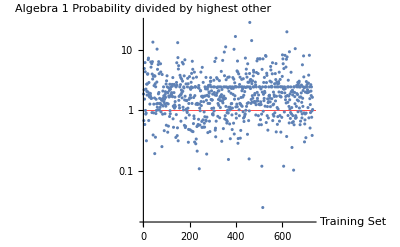

```mathematica
lp=ListLogPlot[#right/#wrong&@ <|"right"-> algebra1IsAlgebra1, "wrong"-> algebra1IsAlgebra2|>,AxesLabel->{"Training Set","Algebra 1 Probability divided by highest other"}, GridLines->{{}, {1}}, GridLinesStyle->Red]
```

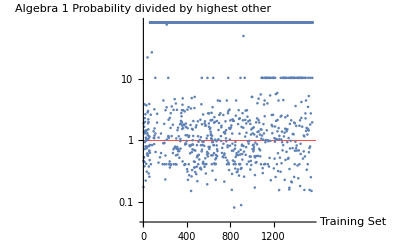

C:\Users\Silas Grossberndt\Documents\GitHub\WSS-Template\Final Project\Drafts\problem_sets\2pset_trained_NeuralNetwork.pdf

```mathematica
lp1=ListLogPlot[#right/#wrong&@ <|"right"-> algebra2IsAlgebra2, "wrong"-> algebra2IsAlgebra1|>,AxesLabel->{"Training Set","Algebra 1 Probability divided by highest other"},GridLines->{{}, {1}}, GridLinesStyle->Red]
Export["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\2pset_trained_NeuralNetwork.pdf", {lp, lp1}]
```

```mathematica
turnOffEquivFrac[question_]:=MatchQ[question, {__, "Fraction",__,"implest form"}];
equivilentFraction[x_, y_, n_]:= n*x/y ;/turnOffEquivFrac==False;
isMatrix[answer_]:=MatchQ[answer, MatrixForm];
allpoints[question_]:=MatchQ[question, {__, "all points", __}];
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d")"}}-> {{"("c, d")"},{"(",a, b, ")"}}
isPoint[answer_]:=MatchQ[answer, {"("__")"}];
commutative[a_,b_]:=a+b-> b+a;
distributive[a_,b_, c_]:=a*(b+c)-> a*b+a*c/; isMatrix==False;
commutativemulti[a_, b_]:=a*b-> b*a;/;isMatrix==False;
associative[a_, b_, c_]:=a+(b+c)-> (a+b)+c;
associativemulti[a_, b_,c_]:=a*(b*c)-> (a*b)*c;
sin2[x_]:=Sin[x]-> 2Sin[x/2]Cos[x/2];
cos2[x_]:=Cos[x]-> Power[Cos[x/2], 2]*2-1;
cos2alt1[x_]:=Cos[x]-> -1Power[Sin[x/2], 2]*2+1;
cos2alt2[x_]:=Cos[x]-> Power[Cos[x/2], 2]-Power[Sin[x/2], 2]
```

```mathematica
(*include the above graphs and the test functions to show infeasiability of doing the classifier*)

questionClassifier["Derivative of f(x)=x^2"]
questionClassifier["Integral of x dx"]

questionClassifier["What is 10% of 110", {"Probabilities"}]

questionClassifier["sin(π/5)"]
(*Need to add more training about sine to a2, derivative to calc*)

questionClassifier["35+3"]
questionClassifier["Derivative of x^6", {"Probabilities"}]
ClassifierMeasurements[questionClassifier, <|"algebra 1"-> algebra1Questions,"algebra 2"-> algebra2Qs |>,"Accuracy"]
```

algebra 1

algebra 1

{<|algebra 1→0.583546,algebra 2→0.416454|>}

algebra 2

algebra 1

{<|algebra 1→0.583546,algebra 2→0.416454|>}

0.785402

```mathematica
algebra2Qs⟦120⟧
```

\r

```mathematica
%51
```

https://math.ly/api/v1/calculus/polynomial-differentiation.json

```mathematica
"<math><mfrac><mo>&DifferentialD;</mo><mrow><mo>&DifferentialD;</mo><mi>x</mi></mrow></mfrac><mo> ( </mo><mrow><mo> - </mo><mn>5</mn></mrow><msup><mi>x</mi><mn>3</mn></msup><mo> - </mo><mn>5</mn><msup><mi>x</mi><mn>2</mn></msup><mo> - </mo><mn>3</mn><mi>x</mi><mo> - </mo><mn>4</mn><mo> ) </mo></math>"
```

<math><mfrac><mo>&DifferentialD;</mo><mrow><mo>&DifferentialD;</mo><mi>x</mi></mrow></mfrac><mo> ( </mo><mrow><mo> - </mo><mn>5</mn></mrow><msup><mi>x</mi><mn>3</mn></msup><mo> - </mo><mn>5</mn><msup><mi>x</mi><mn>2</mn></msup><mo> - </mo><mn>3</mn><mi>x</mi><mo> - </mo><mn>4</mn><mo> ) </mo></math>

```mathematica
Interpreter["MathMLExpression"]["<math>
<mfrac><mo>&DifferentialD;</mo>
<mrow>
<mo>&DifferentialD;</mo>
<mi>x</mi>
</mrow>
</mfrac>
<mo> ( </mo>
<mrow>
<mo> -</mo><mn>5</mn></mrow><msup><mi>x</mi><mn>3</mn></msup><mo> - 
</mo><mn>5</mn><msup><mi>x</mi><mn>2</mn></msup><mo> - 
</mo><mn>3</mn><mi>x</mi><mo> - </mo><mn>4</mn><mo> ) </mo>

</math>"]
```

Failure[…]

```mathematica
questionClassifier["A salesman is paid a monthly salary of $200 plus 6% commission on his monthly sales.\nDetermine the amount of sales required for his total monthly income to be $5."]
```

algebra 1

```mathematica
(*Have a working classifier on algebra 1 and 2, to add calc would need an extra data set*)
```

```mathematica
correctAnswer[answer_, correct_]:=MatchQ[answer, correct]
setLevel[question_, tag_]:=If[UnsameQ[tag, ""], tag, questionClassifier[question]]
```

```mathematica
tagAssociations:=<|"algebra 1"-> {commutativeAddition, commutativemulti, distributive, associative, associativemulti, equivilentFraction, 
(*Need to put theorem prover in, apply tags to state what theorems go to what
```

```mathematica
equivilentAnswer[question_,tag_, answer_, correct_, x_]:= If[correctAnswer[answer, correct]==False, 
If[
	turnOffEquivFrac[question], False, 
	qTag=SetLevel[question, tag];
	If[MatchQ[qTag, "calc"], 
	If[Series[answer, {x,0, 6}]==Series[correct, {x, 0, 6}], True, False],
```

```mathematica
ImportString[%99, "MathML"] //RawBoxes
```

ⅆ/ⅆx(-5 x^3-5 x^2-3x-4)

```mathematica
pDiffProblem=Import[polydiffurl, "Data"]⟦2⟧;
```

FetchURL::httperr: The request to URL https://math.ly/api/v1/calculus/polynomial-differentiation.json was not successful. The server returned the HTTP status code 429.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

```mathematica
strippedQuestion="question"/.pDiffProblem;
```

XML`Parser`XMLGetString::prserr: Expected comment or processing instruction at Line: 1 Character: 87.

```mathematica
strippedQuestion="<math>"<>strippedQuestion<>"</math>";
```

```mathematica
ImportString[strippedQuestion, "MathML"] //RawBoxes;
```

XML`Parser`XMLGetString::prserr: Expected end of tag 'mo' at Line: 1 Character: 171.

{ⅆ/ⅆx(10+10 x^-1-9 x^-2),ⅆ/ⅆx(4 x^2-11x+4),ⅆ/ⅆx(12+3 x^-1+3 x^-2),ⅆ/ⅆx(-5 x^3-5 x^2-3x-4)}

```mathematica
For[i=0, i<10, i++, pDiffProblem=Import[polydiffurl, "Data"]⟦2⟧;
strippedQuestion="question"/.pDiffProblem; strippedQuestion="<math>"<>strippedQuestion<>"</math>";
is=ImportString[strippedQuestion, "MathML"] //RawBoxes; If[is≠$Failed, AppendTo[pDiffStorage, is]]];
(*Wait for a new IP address, this one is 429'ed*)
```

FetchURL::httperr: The request to URL https://math.ly/api/v1/calculus/polynomial-differentiation.json was not successful. The server returned the HTTP status code 429.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringJoin::string: String expected at position 2 in <math><>(question/.$Failed⟦2⟧)<></math>.

ImportString::string: First argument <math><>(question/.$Failed⟦2⟧)<></math> is not a string.

FetchURL::httperr: The request to URL https://math.ly/api/v1/calculus/polynomial-differentiation.json was not successful. The server returned the HTTP status code 429.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringJoin::string: String expected at position 2 in <math><>(question/.$Failed⟦2⟧)<></math>.

ImportString::string: First argument <math><>(question/.$Failed⟦2⟧)<></math> is not a string.

FetchURL::httperr: The request to URL https://math.ly/api/v1/calculus/polynomial-differentiation.json was not successful. The server returned the HTTP status code 429.

General::stop: Further output of FetchURL::httperr will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {$Failed⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in <math><>(question/.$Failed⟦2⟧)<></math>.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

ImportString::string: First argument <math><>(question/.$Failed⟦2⟧)<></math> is not a string.

General::stop: Further output of ImportString::string will be suppressed during this calculation.

```mathematica
getPDiffProblems
```

```mathematica
pDiffStorage
```

{ⅆ/ⅆx(10+10 x^-1-9 x^-2),ⅆ/ⅆx(4 x^2-11x+4),ⅆ/ⅆx(12+3 x^-1+3 x^-2),ⅆ/ⅆx(-5 x^3-5 x^2-3x-4),ⅆ/ⅆx(-6 x^-1+4 x^-2)}

```mathematica
pDiffStorage=pDiffStorage[[1;;5]]
```

{ⅆ/ⅆx(10+10 x^-1-9 x^-2),ⅆ/ⅆx(4 x^2-11x+4),ⅆ/ⅆx(12+3 x^-1+3 x^-2),ⅆ/ⅆx(-5 x^3-5 x^2-3x-4),ⅆ/ⅆx(-6 x^-1+4 x^-2)}

```mathematica
polydiffurl
```

https://math.ly/api/v1/calculus/polynomial-differentiation.json

```mathematica
trigdiffurl="https://math.ly/api/v1/calculus/trigonometric-differentiation.json"
```

https://math.ly/api/v1/calculus/trigonometric-differentiation.json

```mathematica
expodiffurl="https://math.ly/api/v1/calculus/exponents-differentiation.json"
```

https://math.ly/api/v1/calculus/exponents-differentiation.json

```mathematica
polyinturl="https://math.ly/api/v1/calculus/polynomial-integration.json"
```

https://math.ly/api/v1/calculus/polynomial-integration.json

```mathematica
triginturl="https://math.ly/api/v1/calculus/trignometric-integration.json"
```

https://math.ly/api/v1/calculus/trignometric-integration.json

```mathematica
trigdefinturl="https://math.ly/api/v1/calculus/trignometric-definite-integration.json"
```

https://math.ly/api/v1/calculus/trignometric-definite-integration.json

```mathematica
expointurl="https://math.ly/api/v1/calculus/exponents-integration.json"
expodefinturl="https://math.ly/api/v1/calculus/exponents-definite-integration.json"
```

https://math.ly/api/v1/calculus/exponents-integration.json

https://math.ly/api/v1/calculus/exponents-definite-integration.json

```mathematica
polydefinturl="https://math.ly/api/v1/calculus/polynomial-definite-integration.json"
```

https://math.ly/api/v1/calculus/polynomial-definite-integration.json

```mathematica
getcalcPs[url_, dataarray_]:=For[i=0, i<10, i++, pDiffProblem=Import[url, "Data"]⟦2⟧;
strippedQuestion="question"/.pDiffProblem; strippedQuestion="<math>"<>strippedQuestion<>"</math>";
is=ImportString[strippedQuestion, "MathML"] //RawBoxes; If[is≠$Failed, AppendTo[dataarray, is]]];
```

```mathematica
urls={polydefinturl, polydiffurl, polyinturl, trigdefinturl, trigdiffurl, triginturl, expodefinturl, expodiffurl, expointurl}
```

{https://math.ly/api/v1/calculus/polynomial-definite-integration.json,https://math.ly/api/v1/calculus/polynomial-differentiation.json,https://math.ly/api/v1/calculus/polynomial-integration.json,https://math.ly/api/v1/calculus/trignometric-definite-integration.json,https://math.ly/api/v1/calculus/trigonometric-differentiation.json,https://math.ly/api/v1/calculus/trignometric-integration.json,https://math.ly/api/v1/calculus/exponents-definite-integration.json,https://math.ly/api/v1/calculus/exponents-differentiation.json,https://math.ly/api/v1/calculus/exponents-integration.json}

```mathematica
pdefint={"integral of x^6 dx from 0 to 1"}
```

{a}

```mathematica
pint={"integral of x^3 dx"}
```

{integral of x^3 dx}

```mathematica
tint={"integral of cos(x) dx"};
tdefint={"integral of tan(x) dx from 0 to π/4"}
```

{integral of tan(x) dx from 0 to π/4}

```mathematica
tdiff={"Derivative of 1+sec(x)"}
```

{Derivative of 1+sec(x)}

```mathematica
expodefint={"Integral of ln(x) from 1 to e"};
expodiff={"Derivative of e^(3 SuperscriptBox[x, 2])"}
```

{Derivative of e^(3 SuperscriptBox[x, 2])}

```mathematica
expoint={"Integral of ln(1-x)/x dx"}
```

{Integral of ln(1-x)/x dx}

```mathematica
arrays={pdefint, pDiffStorage, pint, tdefint, tdiff, tint, expodefint, expodiff, expoint}
```

{{a},{ⅆ/ⅆx(10+10 x^-1-9 x^-2),ⅆ/ⅆx(4 x^2-11x+4),ⅆ/ⅆx(12+3 x^-1+3 x^-2),ⅆ/ⅆx(-5 x^3-5 x^2-3x-4),ⅆ/ⅆx(-6 x^-1+4 x^-2)},{integral of x^3 dx},{integral of tan(x) dx from 0 to π/4},{Derivative of 1+sec(x)},{integral of cos(x) dx},{Integral of ln(x) from 1 to e},{Derivative of e^(3 SuperscriptBox[x, 2])},{Integral of ln(1-x)/x dx}}

```mathematica
getcalcPs[urls⟦1⟧, arrays⟦1⟧]; (*429 again on all, need a new IP*)
```

FetchURL::httperr: The request to URL https://math.ly/api/v1/calculus/polynomial-definite-integration.json was not successful. The server returned the HTTP status code 404 ("Not Found").

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringJoin::string: String expected at position 2 in <math><>(question/.$Failed⟦2⟧)<></math>.

ImportString::string: First argument <math><>(question/.$Failed⟦2⟧)<></math> is not a string.

FetchURL::httperr: The request to URL https://math.ly/api/v1/calculus/polynomial-definite-integration.json was not successful. The server returned the HTTP status code 404 ("Not Found").

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringJoin::string: String expected at position 2 in <math><>(question/.$Failed⟦2⟧)<></math>.

ImportString::string: First argument <math><>(question/.$Failed⟦2⟧)<></math> is not a string.

FetchURL::httperr: The request to URL https://math.ly/api/v1/calculus/polynomial-definite-integration.json was not successful. The server returned the HTTP status code 404 ("Not Found").

General::stop: Further output of FetchURL::httperr will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {$Failed⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in <math><>(question/.$Failed⟦2⟧)<></math>.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

ImportString::string: First argument <math><>(question/.$Failed⟦2⟧)<></math> is not a string.

General::stop: Further output of ImportString::string will be suppressed during this calculation.

```mathematica
pint
```

{integral of x^3 dx}